```mathematica
Reduce[Floor[Pi*10^x]==6, x, Reals]
Reduce[Floor[Pi/ArcTan[10^(-x)]]==13, x, Reals]
```

(Log[2]+Log[3]-Log[π])/(Log[2]+Log[5])≤x<(Log[7]-Log[π])/(Log[2]+Log[5])

-Log[Tan[π/13]]/(Log[2]+Log[5])≤x<-Log[Tan[π/14]]/(Log[2]+Log[5])

```mathematica
min:=Log[n/Pi]/Log[10]
max:=-Log[Tan[Pi/(n+1)]]/Log[10]
```

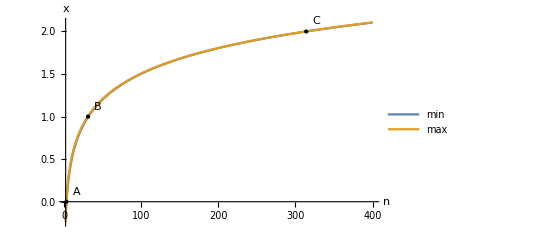

```mathematica
With[{},
pt1={3, 0};
pt2={31, 1};
pt3={314, 2};];
Plot[{min, max}, {n, 2, 400},Epilog->{Directive[{Thick,Red,Dashed}], Black,PointSize[Large],
{Point[pt1], Point[pt2], Point[pt3]},
{Text["A",Offset[{10,10},pt1]],
Text["B",Offset[{10,10},pt2]],
Text["C",Offset[{10,10},pt3]]}
},AxesLabel->{"n","x"},PlotLabel->"",LabelStyle->Black, PlotLegends->"Expressions"]
```

```mathematica
Sum[Sin[2*k*Pi*x]/k, {k, 1, Infinity}]
```

1/2 ⅈ (Log[1-ⅇ^(2 ⅈ π x)]-Log[ⅇ^(-2 ⅈ π x) (-1+ⅇ^(2 ⅈ π x))])

```mathematica
Simplify[1/2 ⅈ (Log[1-ⅇ^(2 ⅈ π x)]-Log[ⅇ^(-2 ⅈ π x) (-1+ⅇ^(2 ⅈ π x))])]
```

1/2 ⅈ (-Log[1-ⅇ^(-2 ⅈ π x)]+Log[1-ⅇ^(2 ⅈ π x)])

```mathematica
FloorFunc[x_]:=-1/2+x+1/(2*Pi) ⅈ (-Log[1-E^(-2 ⅈ Pi x)]+Log[1-E^(2 ⅈ Pi x)])
Simplify[(FloorFunc[Sqrt[n*Pi/2]]+k)*(FloorFunc[Sqrt[n*Pi/2]]+k-1)] (*< n Pi/2*)
%*4Pi^2 (*<2 n Pi^3*)
Func[n_]=Simplify[ExpandAll[%]-2 n Pi^3] (*<0*)

sols:=Solve[Func[n]==0, k]
lim:=Limit[Func[n], k->0]

Text["Zeroes of parabola"]
firstZero=k/.Simplify[Part[sols, 1]]
secondZero=k/.Simplify[Part[sols, 2]]
vertex=Simplify[lim]

(*Text["Values of a, b, c, in ax^2+bx+c of parabola"]
solutions:=Solve[{c==vertex, a*firstZero^2+b*firstZero+c==0, a*secondZero^2+b*secondZero+c==0}, {a, b, c}]
solA=Simplify[a/.Part[solutions, 1]]
solB=Simplify[b/.Part[solutions, 1]]
solC=Simplify[c/.Part[solutions, 1]]*)

Plot[secondZero, {n, 0, 50}]
```

(-3/2+k+√n √(π/2)+(ⅈ Log[-ⅇ^(ⅈ √2 √n π^(3/2))])/(2 π)) (-1/2+k+√n √(π/2)+(ⅈ Log[-ⅇ^(ⅈ √2 √n π^(3/2))])/(2 π))

π^2 (3+4 k^2-4 √n √(2 π)+4 k (-2+√n √(2 π)))+2 ⅈ π (-2+2 k+√n √(2 π)) Log[-ⅇ^(ⅈ √2 √n π^(3/2))]-Log[-ⅇ^(ⅈ √2 √n π^(3/2))]^2

-(π (-2+√n √(2 π)+√(1+2 n π))+ⅈ Log[-ⅇ^(ⅈ √2 √n π^(3/2))])/(2 π)

(π (2-√n √(2 π)+√(1+2 n π))-ⅈ Log[-ⅇ^(ⅈ √2 √n π^(3/2))])/(2 π)

π^2 (3-4 √n √(2 π))+2 ⅈ π (-2+√n √(2 π)) Log[-ⅇ^(ⅈ √2 √n π^(3/2))]-Log[-ⅇ^(ⅈ √2 √n π^(3/2))]^2

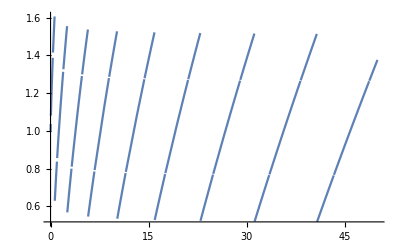

```mathematica
FloorF[x_]:=-1/2+x+ⅈ*Log[-E^(2*ⅈ*Pi*x)]/(2*Pi)
Expr[n_]=(FloorF[Sqrt[n*Pi/2]]+k)*(FloorF[Sqrt[n*Pi/2]]+k-1) (*<nPi/2*)
Func[n_, k_]=Simplify[ExpandAll[Expr[n]]-n*Pi/2]*4*Pi^2 (*<0*)
zeroes:=Solve[Func[n, k]==0, k]
firstZero=Simplify[k/.Part[zeroes, 1]]
secondZero=Simplify[k/.Part[zeroes, 2]]
vertex=Simplify[Limit[Func[n, k], k->0]]
Plot[secondZero, {n, 0, 50}]
```

```mathematica
(π (2-Sqrt[n] Sqrt[2 π]+Sqrt[1+2 n π]))/(2 π)-(I Log[-E^(I Sqrt[2] Sqrt[n] π^(3/2))])/(2 π)
```

1/2 (2-√n √(2 π)+√(1+2 n π))-(ⅈ Log[-ⅇ^(ⅈ √2 √n π^(3/2))])/(2 π)

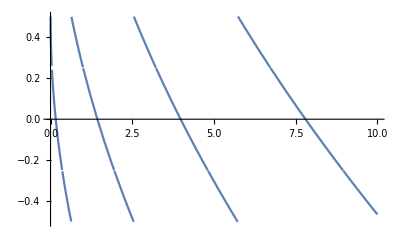

```mathematica
Plot[(I Log[-E^(I Sqrt[2] Sqrt[n] π^(3/2))])/(2Pi), {n, 0, 10}]
```